```mathematica
Table[
With[{g=ReadGrof[k]},
{k,ChromaticPolynomial[g,4]/24}->Sort[Tally[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}]]]
]
,{k,100}
]//TableForm
```

{1,1}→{{2,6}}
{2,1}→{{2,6},{3,3}}
{3,1}→{{2,7},{3,4},{5,1}}
{4,4}→{{5,12}}
{5,1}→{{2,8},{3,5},{5,2}}
{6,4}→{{5,9},{6,3},{8,3}}
{7,5}→{{6,10},{9,5}}
{8,1}→{{2,8},{3,6},{9,1}}
{9,1}→{{2,9},{3,3},{5,3}}
{10,1}→{{2,9},{3,6},{5,3}}
{11,5}→{{6,8},{7,2},{9,4},{10,3},{13,1}}
{12,1}→{{2,9},{3,6},{5,3}}
{13,1}→{{2,9},{3,7},{5,1},{9,1}}
{14,4}→{{5,9},{6,2},{8,5},{12,2}}
{15,4}→{{5,6},{6,6},{8,6}}
{16,1}→{{2,10},{3,5},{5,2},{9,1}}
{17,1}→{{2,10},{3,4},{5,4}}
{18,3}→{{4,4},{7,8},{8,6}}
{19,4}→{{5,6},{6,6},{8,6}}
{20,4}→{{5,7},{6,4},{8,7}}
{21,12}→{{13,12},{17,6}}
{22,1}→{{2,9},{3,8},{17,1}}
{23,1}→{{2,12},{5,6}}
{24,1}→{{2,10},{3,8},{5,2},{9,1}}
{25,4}→{{5,6},{6,5},{8,8},{12,2}}
{26,5}→{{6,8},{7,2},{9,4},{10,4},{15,2},{21,1}}
{27,1}→{{2,10},{3,7},{5,4}}
{28,1}→{{2,10},{3,7},{5,4}}
{29,1}→{{2,10},{3,8},{5,2},{9,1}}
{30,4}→{{5,9},{6,2},{8,6},{12,3},{20,1}}
{31,5}→{{6,6},{7,4},{9,3},{10,6},{13,2}}
{32,1}→{{2,11},{3,6},{5,3},{9,1}}
{33,1}→{{2,11},{3,5},{5,5}}
{34,1}→{{2,11},{3,6},{5,3},{9,1}}
{35,4}→{{5,6},{6,5},{8,8},{12,2}}
{36,3}→{{4,4},{6,3},{7,6},{8,5},{11,2},{13,1}}
{37,12}→{{13,10},{14,2},{17,5},{22,1},{24,3}}
{38,3}→{{4,3},{5,1},{6,3},{7,7},{8,5},{11,1},{13,1}}
{39,5}→{{6,8},{7,1},{9,5},{10,4},{13,1},{15,2}}
{40,9}→{{10,4},{12,4},{13,6},{14,4},{21,3}}
{41,6}→{{7,2},{9,6},{10,4},{11,8},{18,1}}
{42,5}→{{6,7},{7,2},{9,4},{10,6},{13,2}}
{43,5}→{{6,6},{7,4},{9,3},{10,6},{13,2}}
{44,5}→{{6,6},{7,4},{9,3},{10,6},{13,2}}
{45,5}→{{6,6},{7,4},{9,4},{10,6},{21,1}}
{46,2}→{{5,12},{6,3},{7,6}}
{47,1}→{{2,10},{3,8},{5,2},{9,1}}
{48,1}→{{2,10},{3,7},{5,4}}
{49,4}→{{5,6},{6,5},{8,8},{12,2}}
{50,1}→{{2,10},{3,8},{5,2},{9,1}}
{51,1}→{{2,11},{3,7},{5,1},{9,2}}
{52,1}→{{2,11},{3,5},{5,5}}
{53,1}→{{2,11},{3,6},{5,3},{9,1}}
{54,1}→{{2,10},{3,9},{5,1},{17,1}}
{55,1}→{{2,10},{3,9},{9,2}}
{56,4}→{{5,9},{6,2},{8,5},{12,5}}
{57,4}→{{5,7},{6,3},{8,9},{12,2}}
{58,1}→{{2,11},{3,6},{5,3},{9,1}}
{59,1}→{{2,11},{3,7},{5,2},{17,1}}
{60,1}→{{2,11},{3,7},{5,1},{9,2}}
{61,1}→{{2,11},{3,6},{5,3},{9,1}}
{62,16}→{{18,3},{20,18}}
{63,4}→{{5,9},{6,1},{8,8},{12,2},{20,1}}
{64,4}→{{5,7},{6,4},{8,7},{12,3}}
{65,4}→{{5,5},{6,5},{8,11}}
{66,4}→{{5,3},{6,9},{8,9}}
{67,4}→{{5,4},{6,7},{8,10}}
{68,1}→{{2,11},{3,7},{5,2},{17,1}}
{69,1}→{{2,13},{3,2},{5,5},{9,1}}
{70,1}→{{2,12},{3,4},{5,4},{9,1}}
{71,1}→{{2,12},{3,5},{5,2},{9,2}}
{72,21}→{{22,14},{33,7}}
{73,1}→{{2,10},{3,10},{33,1}}
{74,1}→{{2,11},{3,9},{5,3},{9,1}}
{75,1}→{{2,11},{3,9},{5,3},{9,1}}
{76,5}→{{6,8},{7,1},{9,5},{10,5},{13,1},{15,3},{25,1}}
{77,1}→{{2,11},{3,10},{5,1},{9,2}}
{78,4}→{{5,9},{6,2},{8,6},{12,6},{20,1}}
{79,4}→{{5,6},{6,5},{8,9},{12,3},{20,1}}
{80,12}→{{13,8},{14,4},{17,4},{22,2},{24,6}}
{81,1}→{{2,11},{3,10},{5,2},{17,1}}
{82,4}→{{5,7},{6,2},{8,11},{12,4}}
{83,1}→{{2,12},{3,7},{5,4},{9,1}}
{84,1}→{{2,12},{3,8},{5,3},{17,1}}
{85,1}→{{2,12},{3,8},{5,2},{9,2}}
{86,1}→{{2,12},{3,7},{5,4},{9,1}}
{87,1}→{{2,11},{3,9},{5,3},{9,1}}
{88,3}→{{4,3},{5,1},{6,4},{7,7},{8,5},{9,2},{13,1},{19,1}}
{89,5}→{{6,6},{7,4},{9,3},{10,7},{13,1},{15,2},{21,1}}
{90,5}→{{6,6},{7,3},{9,4},{10,7},{13,2},{15,2}}
{91,9}→{{10,4},{12,3},{13,4},{14,4},{15,1},{17,2},{18,3},{21,3}}
{92,1}→{{2,11},{3,8},{5,5}}
{93,4}→{{5,6},{6,5},{8,9},{12,3},{20,1}}
{94,3}→{{4,2},{5,2},{6,6},{7,6},{8,4},{11,2},{13,2}}
{95,4}→{{5,6},{6,4},{8,10},{12,4}}
{96,4}→{{5,6},{6,4},{8,10},{12,4}}
{97,4}→{{5,6},{6,5},{8,8},{12,5}}
{98,16}→{{18,3},{20,15},{24,3},{32,3}}
{99,3}→{{4,4},{6,4},{7,6},{8,5},{9,2},{11,2},{23,1}}
{100,5}→{{6,6},{7,3},{9,4},{10,7},{13,2},{15,2}}

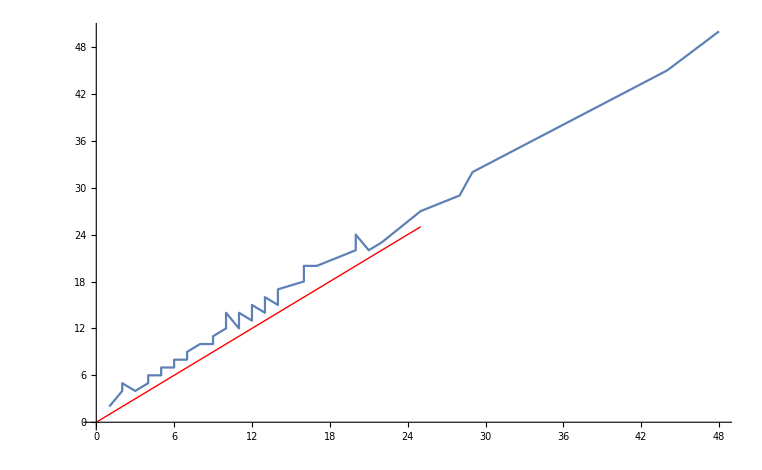

```mathematica
Show[Monitor[
Table[
With[{g=ReadGrof[k]},
{ChromaticPolynomial[g,4]/24,Min[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}]]}
]
,{k,1000}
]
,{k,e}]
//DeleteDuplicates//Sort//ListLinePlot,
Plot[x,{x,0,25}, PlotStyle->Directive[Thick,Red]]
]
```

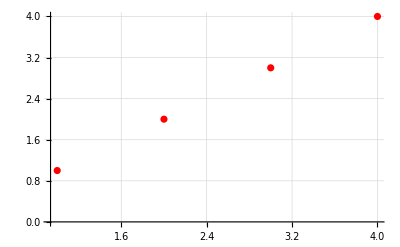

```mathematica
ListPlot[Monitor[
Table[
With[{g=ReadGrof[k]},
Min[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}]]-ChromaticPolynomial[g,4]/24
]
,{k,1000}
]
,{k,e}]//DeleteDuplicates//Sort,
PlotRange->All,
GridLines->Automatic,
PlotStyle->Directive[Thick,Red]
]
```

```mathematica
Monitor[
Table[
With[{g=ReadGrof[k]},
Min[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}]]-ChromaticPolynomial[g,4]/24
]
,{k,1000}
]
,{k,e}]//Tally//Sort
```

{{1,904},{2,78},{3,9},{4,9}}

```mathematica
Monitor[
Table[
With[{g=ReadGrof[k]},
Min[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}]]-ChromaticPolynomial[g,4]/24
]
,{k,10000}
]
,{k,e}]//Tally//Sort
```

{{1,8866},{2,759},{3,163},{4,193},{5,15},{6,1},{8,3}}

```mathematica
VertexCount[ReadGrof[300000]]
```

14

```mathematica
Monitor[
Table[
With[{g=ReadGrof[k]},
Min[Table[ChromaticPolynomial[EdgeDelete[g,e],4]/24,{e,EdgeList[g]}]]-ChromaticPolynomial[g,4]/24
]
,{k,300000}
]
,{k,e}]//Tally//Sort
```